Re-digitalization by Can Yesilyurt 27 Nov 2020

Image input
Must be clear from any inset/numbers/text. Middle axis is ok.

Raw image for comparison
Taken from Berdyugin et al., Science 364, 162–165 (2019)

```mathematica
img=-Graphics-;
```

Frame labels and range parameters

```mathematica
Xmin=-40.;
Xmax=40.;
Ymin=-7.;
Ymax=7.;
Xtext="Magnetic Field, B (mT)";
Ytext="Hall viscosity νH";
```

Compute

```mathematica
d=ImageDimensions[img];
img=Inpaint[img,Binarize[ImageResize[CrossMatrix[(d-1)/11] //Image,d]] ];
dc=DominantColors[img];
dcNW=Drop[dc,Flatten[Position[dc,RGBColor[1., 0.9999720990932929, 0.9997781770702426, 1.]]]];
plots=Binarize[ColorNegate[ColorDetect[img,dcNW[[#]]]]]&/@Range[1,Length[dcNW]];
JJ={};
For[i=1,i<=Length[plots],i++,
bpl=Binarize[plots[[i]],0.0000001];
j=Position[ImageData[bpl,DataReversed->True],0];
AppendTo[JJ,j];
]
out={};
For[in=1,in<=Length[plots],in++,
b=JJ[[in]][[;;,1]];
bb=((Ymax-Ymin)*(b/(Max[Flatten[JJ[[1]][[;;,1]]]]-Min[Flatten[JJ[[1]][[;;,1]]]])))+Ymin;
bb=DeleteDuplicates[bb];
aa=Range[Xmin,Xmax,(Xmax-Xmin)/Length[bb]];
o={aa[[#]],bb[[#]]}&/@Range[1,Length[bb]];
AppendTo[out,o];
]
AR=ImageDimensions[img][[1]]/ImageDimensions[img][[2]]*1.0;
p1=ListPlot[out,AspectRatio->1/AR,Frame->True,FrameLabel->{Xtext,Ytext},LabelStyle->Directive[Black,16],PlotStyle->dcNW,ImageSize->Medium,Axes->False]
```

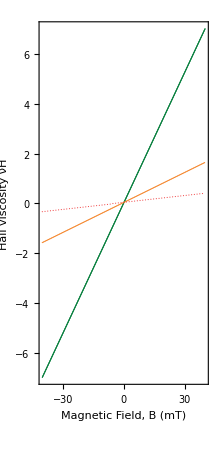
```mathematica
-Graphics-                  -Graphics-
Berdyugin et al., Science 364, 162–165 (2019)
```